```mathematica
(*Vb = Jb1(t)t1dot + ... + Jbn(t)tndot
Jbi = (wbi, vbi) example: 5.3 screw vector expressed in coordinates of end-effector frame. 
K= VbGbVb *)
```

```mathematica
v1 = {0,L1,0}
w1 = {0,0,1}
w1b = Dot[RotationMatrix[-θ2,{1,0,0}],{0,0,1}]
w2b = {1,0,0}
v1b = -Cross[w1b,{-L1,0,L2}]
v2b={0,L2,0}
```

{0,L1,0}

{0,0,1}

```mathematica
{0,Sin[θ2],Cos[θ2]}
```

{1,0,0}

{-L2 Sin[θ2],L1 Cos[θ2],-L1 Sin[θ2]}

{0,L2,0}

```mathematica
Jb1 = {0,0,1,0,L1,0};
```

```mathematica
Vb1 = Transpose[Jb1]*D[θ1[t],t]
```

{0,0,θ1'[t],0,L1 θ1'[t],0}

```mathematica
w1b
```

{0,Sin[θ2],Cos[θ2]}

```mathematica
Jb1 = Transpose[Join[w1,v1]]
```

{0,0,1,0,L1,0}

```mathematica
Jb2 = {Transpose[Join[w1b,v1b]],Transpose[Join[ w2b,v2b]]}
```

{{0,Sin[θ2],Cos[θ2],-L2 Sin[θ2],L1 Cos[θ2],-L1 Sin[θ2]},{1,0,0,0,L2,0}}

```mathematica
Jb2 = Transpose[Jb2]
```

{{0,1},{Sin[θ2],0},{Cos[θ2],0},{-L2 Sin[θ2],0},{L1 Cos[θ2],L2},{-L1 Sin[θ2],0}}

```mathematica
MatrixForm[Jb2]
```

(0 | 1
Sin[θ2] | 0
Cos[θ2] | 0
-L2 Sin[θ2] | 0
L1 Cos[θ2] | L2
-L1 Sin[θ2] | 0)

```mathematica
Vb1 = Transpose[Vb1]
```

{0,0,θ1'[t],0,L1 θ1'[t],0}

```mathematica
Vb2= Dot[Jb2, {D[θ1[t],t], D[θ2[t],t]}]
```

{θ2'[t],Sin[θ2] θ1'[t],Cos[θ2] θ1'[t],-L2 Sin[θ2] θ1'[t],L1 Cos[θ2] θ1'[t]+L2 θ2'[t],-L1 Sin[θ2] θ1'[t]}

```mathematica
MatrixForm[Vb2]
```

(θ2'[t]
Sin[θ2] θ1'[t]
Cos[θ2] θ1'[t]
-L2 Sin[θ2] θ1'[t]
L1 Cos[θ2] θ1'[t]+L2 θ2'[t]
-L1 Sin[θ2] θ1'[t])

```mathematica
Vb1
```

{0,0,θ1'[t],0,L1 θ1'[t],0}

```mathematica
L1 = 1;
L2 = 1 ;
```

```mathematica
MatrixForm[Vb1]
```

(0
0
θ1'[t]
0
θ1'[t]
0)

```mathematica
MatrixForm[Vb2]
```

(θ2'[t]
Sin[θ2] θ1'[t]
Cos[θ2] θ1'[t]
-Sin[θ2] θ1'[t]
Cos[θ2] θ1'[t]+θ2'[t]
-Sin[θ2] θ1'[t])

```mathematica
I1 = {{0,0,0},{0,4,0},{0,0,4}};
I2 = {{4,0,0},{0,4,0},{0,0,0}};
Z = I1*0
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
t1 = Join[I1,Z];
t2 = Join[Z,m1*IdentityMatrix[3]];
```

```mathematica
Gb1 = Join[Transpose[t1],Transpose[t2]]
```

{{0,0,0,0,0,0},{0,4,0,0,0,0},{0,0,4,0,0,0},{0,0,0,m1,0,0},{0,0,0,0,m1,0},{0,0,0,0,0,m1}}

```mathematica
t3 = Join[I2,Z];
t4 = Join[Z,m2*IdentityMatrix[3]];
```

```mathematica
Gb2 = Join[Transpose[t3],Transpose[t4]]
```

{{4,0,0,0,0,0},{0,4,0,0,0,0},{0,0,0,0,0,0},{0,0,0,m2,0,0},{0,0,0,0,m2,0},{0,0,0,0,0,m2}}

```mathematica
Ke1 = 0.5*(Dot[Dot[Transpose[Vb1],Gb1],Vb1])
```

0.5 (4 θ1'[t]^2+m1 θ1'[t]^2)

```mathematica
Ke2=0.5*(Dot[Dot[Vb2,Transpose[Gb2]],Vb2])
```

0.5 (4 Sin[θ2]^2 θ1'[t]^2+2 m2 Sin[θ2]^2 θ1'[t]^2+4 θ2'[t]^2+m2 (Cos[θ2] θ1'[t]+θ2'[t])^2)

```mathematica
m1 = 2; 
m2 = 2;
```

```mathematica
K1 =Ke1+Ke2
```

3. θ1'[t]^2+0.5 (8 Sin[θ2]^2 θ1'[t]^2+4 θ2'[t]^2+2 (Cos[θ2] θ1'[t]+θ2'[t])^2)

```mathematica
Expand[K1]
```

3. θ1'[t]^2+1. Cos[θ2]^2 θ1'[t]^2+4. Sin[θ2]^2 θ1'[t]^2+2. Cos[θ2] θ1'[t] θ2'[t]+3. θ2'[t]^2

```mathematica
K1 = 4. θ1'[t]^2+3. Sin[θ2]^2 θ1'[t]^2+2. Cos[θ2] θ1'[t] θ2'[t]+3. θ2'[t]^2
```

4. θ1'[t]^2+3. Sin[θ2]^2 θ1'[t]^2+2. Cos[θ2] θ1'[t] θ2'[t]+3. θ2'[t]^2

```mathematica
g =10;
```

```mathematica
P = m2*g*L2(1-Cos[θ2])
```

20 (1-Cos[θ2])

```mathematica
L = K1- P
```

-20 (1-Cos[θ2])+4. θ1'[t]^2+3. Sin[θ2]^2 θ1'[t]^2+2. Cos[θ2] θ1'[t] θ2'[t]+3. θ2'[t]^2

```mathematica
Tau1 = D[Grad[L,{D[θ1[t],t],D[θ2[t],t]}],t]
```

{8. θ1''[t]+6. Sin[θ2]^2 θ1''[t]+2. Cos[θ2] θ2''[t],2. Cos[θ2] θ1''[t]+6. θ2''[t]}

```mathematica
Tau2 = -Grad[L,{θ1,θ2}]
```

{0.,0.+20 Sin[θ2]-6. Cos[θ2] Sin[θ2] θ1'[t]^2+2. Sin[θ2] θ1'[t] θ2'[t]}

```mathematica
Tau = Tau1+Tau2
```

{0.+8. θ1''[t]+6. Sin[θ2]^2 θ1''[t]+2. Cos[θ2] θ2''[t],0.+20 Sin[θ2]-6. Cos[θ2] Sin[θ2] θ1'[t]^2+2. Sin[θ2] θ1'[t] θ2'[t]+2. Cos[θ2] θ1''[t]+6. θ2''[t]}

```mathematica
(*θ1= Pi/4;
θ2= Pi/4;
θ1'[0]= 0;
θ2'[0]= 0;
θ1''[0]= 0;
 θ2''[0]= 0;
 t= 0;*)
(*θ1'[0]= θ1';
θ2'[0]= θ2';
θ1''[0]= θ1'';
 θ2''[0]= θ2'';
t= 0;*)
```

```mathematica
A ={0.+8. θ1''[t]+6. Sin[θ2]^2 θ1''[t]+2. Cos[θ2] θ2''[t],0.+20 Sin[θ2]-6. Cos[θ2] Sin[θ2] θ1'[t]^2+2. Sin[θ2] θ1'[t] θ2'[t]+2. Cos[θ2] θ1''[t]+6. θ2''[t]}
```

{0.+8. θ1''[t]+6. Sin[θ2]^2 θ1''[t]+2. Cos[θ2] θ2''[t],0.+20 Sin[θ2]-6. Cos[θ2] Sin[θ2] θ1'[t]^2+2. Sin[θ2] θ1'[t] θ2'[t]+2. Cos[θ2] θ1''[t]+6. θ2''[t]}

```mathematica
A ={0.+8.θ1''[t]+6. Sin[Pi/4]^2 θ1''[t]+2. Cos[Pi/4] θ2''[t],0.+20 Sin[Pi/4]-6. Cos[Pi/4] Sin[Pi/4] θ1'[t]^2+2. Sin[Pi/4] θ1'[t] θ2'[t]+2.Rationalize[ Cos[Pi/4]] θ1''[t]+6. θ2''[t]}
```

{0.+11. θ1''[t]+1.41421 θ2''[t],14.1421-3. θ1'[t]^2+1.41421 θ1'[t] θ2'[t]+1.41421 θ1''[t]+6. θ2''[t]}

```mathematica
eqns={0.+8.θ1''[t]+6. Sin[Pi/4]^2 θ1''[t]+2. Cos[Pi/4] θ2''[t]==0,0.+20 Sin[Pi/4]-6. Cos[Pi/4] Sin[Pi/4] θ1'[t]^2+2. Sin[Pi/4] θ1'[t] θ2'[t]+2.Rationalize[ Cos[Pi/4]] θ1''[t]+6. θ2''[t]-14.14==0}
```

{0.+11. θ1''[t]+1.41421 θ2''[t]==0,0.00213562-3. θ1'[t]^2+1.41421 θ1'[t] θ2'[t]+1.41421 θ1''[t]+6. θ2''[t]==0}

```mathematica
CEA = CoefficientArrays[eqns,{θ1''[t],θ2''[t]}]
```

{SparseArray[…],SparseArray[…]}

```mathematica
C1 = MatrixForm[CEA[[2]]]
```

(11. | 1.41421
1.41421 | 6.)

```mathematica
Eigenvectors[%8]
```

{{-0.967054,-0.25457},{0.25457,-0.967054}}

```mathematica
Eigenvalues[%8]
```

{11.3723,5.62772}

```mathematica
points = CirclePoints[100];
```

```mathematica
Dimensions[points]
```

{100,2}

```mathematica
C1=Normal[CEA[[2]]]
```

{{11.,1.41421},{1.41421,6.}}

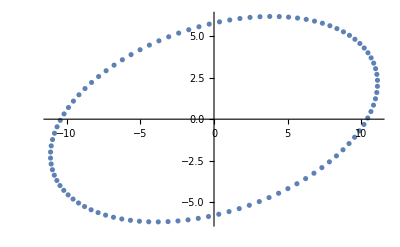

```mathematica
ListPlot[Dot[points,Normal[C1]]]
```

```mathematica
Dot[RotationMatrix[θ1,{0,1,0}],{L2*Cos[θ2],L2*Sin[θ2],1}]
```

{L2 Cos[θ1] Cos[θ2]+Sin[θ1],L2 Sin[θ2],Cos[θ1]-L2 Cos[θ2] Sin[θ1]}

```mathematica
r=MatrixForm[Join[RotationMatrix[θ1,{0,1,0}],{{L1*Cos[θ1]},{L2*Sin[θ1]},{0}},2]]
```

(Cos[θ1] | 0 | Sin[θ1] | L1 Cos[θ1]
0 | 1 | 0 | L2 Sin[θ1]
-Sin[θ1] | 0 | Cos[θ1] | 0)

```mathematica
ArrayFlatten[{{r},{{{0},{0},{0},{1}}}}]
```

{{(Cos[θ1] | 0 | Sin[θ1] | L1 Cos[θ1]
0 | 1 | 0 | L2 Sin[θ1]
-Sin[θ1] | 0 | Cos[θ1] | 0)},{0},{0},{0},{1}}

{1}
 |  |  |  |